```mathematica
(* Teardrop shape for use with magma chambers and blobs. *)
```

```mathematica
teardropFormula:={Cos[t]+Max[0,Cos[t]],Sin[t]*(1-Max[0,Cos[t]]^2)}
```

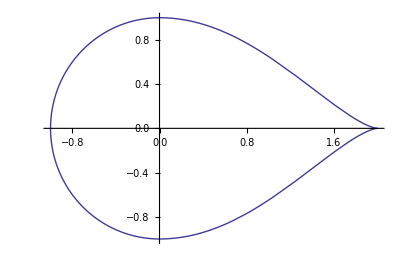

```mathematica
ParametricPlot[teardropFormula,{t,0,2*π}]
```

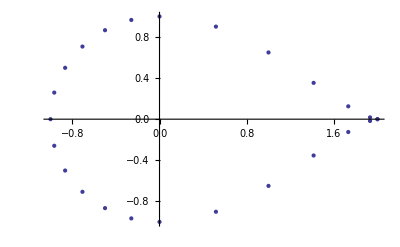

```mathematica
ListPlot[Table[teardropFormula,{t,0,2*π,π/12}]]
```

```mathematica
(* curvature for the subduction angle made up piecewise of lines and arcs *)
```

```mathematica
(* the ideal line is parametereized by t, with t0=0 being placed where the flat portion starts bending down *)
```

```mathematica
t0:=0
```

```mathematica
t1:=θ0*r0
```

```mathematica
t2:=t1+θ1*r1
```

```mathematica
(* c vectors are centers of the arcs that are there *)
```

```mathematica
c0:={d,y0-r0}
```

```mathematica
p0[t_]:= {d-t,y0}
```

```mathematica
p1[t_]:=Module[{θ=π/2+(t-t0)/r0},c0+r0*{Cos[θ],Sin[θ]}]
```

```mathematica
c1:=p1[t1]+r1*Normalize[c0-p1[t1]]
```

```mathematica
p2[t_]:=Module[{θ=π/2+θ0+(t-t1)/r1},c1+r1*{Cos[θ],Sin[θ]}]
```

```mathematica
dir3:=Module[{θ=θ0+θ1+π},{Cos[θ],Sin[θ]}]
```

```mathematica
p3[t_]:=p2[t2]+(t-t2)*dir3
```

```mathematica
rules:={d->2,y0->1,θ0->π/8,r0->4,θ1->π/8,r1->2}
```

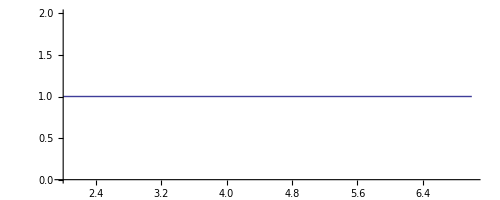

```mathematica
part0=ParametricPlot[p0[t]/.rules,{t,-5,t0}]
```

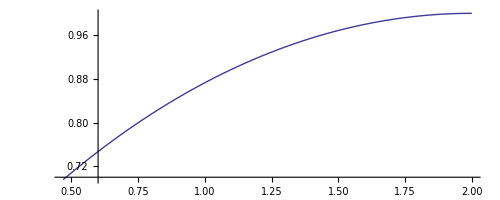

```mathematica
part1=ParametricPlot[p1[t]/.rules,{t,t0,t1/.rules}]
```

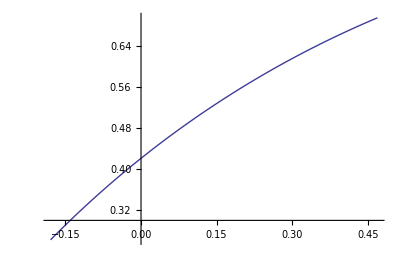

```mathematica
part2=ParametricPlot[p2[t]/.rules,{t,t1/.rules,t2/.rules}]
```

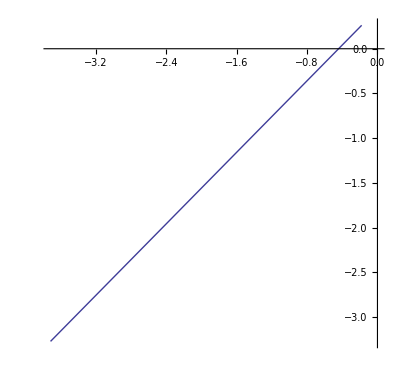

```mathematica
part3=ParametricPlot[p3[t]/.rules,{t,t2/.rules,(t2+5)/.rules}]
```

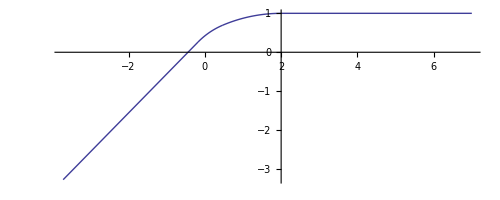

```mathematica
Show[part0,part1,part2,part3,PlotRange->All]
```